Two Photon and Nonlinear refraction Dispersion AlxGa1-xAs- Figure of Merit
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
 see :-
  M. J. LaGasse et al “Femtosecond measurements of the nonresonant nonlinear index in AlGAAs”, Apple Phys. Lett., 56 417-419-1990
 Sheik Bahae et al “Dispersion of bound electronic nonlinear refraction in solids “, IEEE Journal of Quantum Electronics 1991 27 1296-1309.
 E. W. Vanstryland, H. Vanherzeele, M. A. Woodall, M. J. Soileau, A. L. Smirl, S. Guha, et al., “2 Photon-Absorption, Nonlinear Refraction, and Optical Limiting in Semiconductors,” Optical Engineering, vol. 24, pp. 613-623, 1985  http://dx.doi.org/10.1117/12.7973538
 The conversion of units from ESU to SI for n2 can be found at:-
 https://www.rp-photonics.com/nonlinear_index.html
 The dependence of the Al_x Ga_(1-x)As alloy band-gap on x can be found at:-
http://www.semiconductors.co.uk/eg(algaas).htm

Wavelength (double band-gap) = 1478.63 nm   Al fraction = 0.18

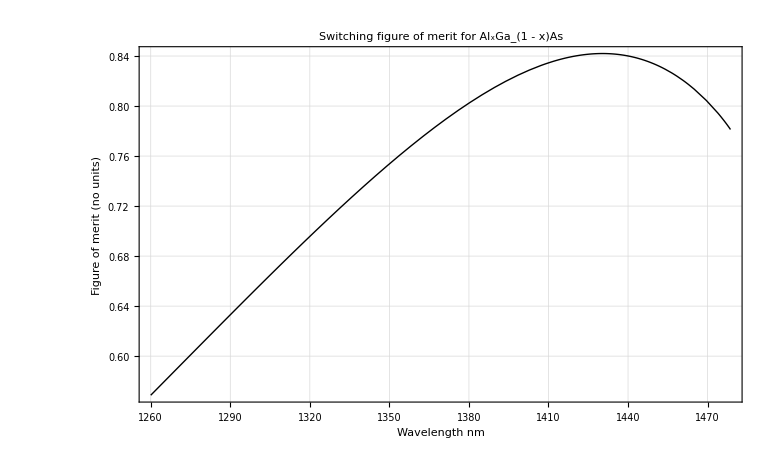

```mathematica
ClearAll[x,CLight,Echarge,PlanckCon,G2,F1]
x=0.18 ;(*input Subscript[Al, x] Subscript[Ga, 1-x] As alloy Al fraction - don't go above x=0.44 or it goes indirect and all bets are off*) 
CLight:=299792458 (*speed of light m/s*)
PlanckCon:=6.6×10^-34(*Planck's constant SI units*)
Echarge:=1.6×10^-19(*Charge on the electron, C*)
EG=1.42 +1.429 x-0.14 x^2 ; (*band gap in eV*)
eV:=(PlanckCon*CLight)/(Echarge(λ×10^-9));(* wavelength, λ, in nm*)
Egλ2:=(PlanckCon×CLight)/(Echarge ×EG)×10^9×2
Print["Wavelength (double band-gap) = ",Egλ2, " nm", "   Al fraction = ",x]
y=eV/EG; (*required for n2 nonlinear refractive index*)
y2=(2 eV)/EG;(*required for β2 two photon absorption coefficient*)
G2=(-2+6y-3 y^2-y^3-3/4 y^4+2(1-2 y)^(3/2)UnitStep[1-2y])/(64 y^6);(*Dispersion of n2 nonlinear refractive index*)
F1=(y2-1)^(3/2)/y2^5;(*Dispersion of β2 nonlinear absorption coefficient*)
BackgroundLoss:=.10 (*wavelength independent loss*)
FigureofMerit:=G2/(F1+BackgroundLoss);
Plot [FigureofMerit,{λ,1260, Egλ2},PlotRange->All,Frame->True,PlotLabel->"Switching figure of merit for Al_xGa_(1 - x)As",AxesStyle->Thin,GridLines->Automatic, PlotStyle->{Directive[Thick,Black]},LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{" Wavelength nm","Figure of merit (no units)"},FrameStyle->Thick]
```